```mathematica
FloatValue[Float[b_,d_,e_]]:=∑_(n=1)^Length[d] d⟦n⟧b^(-(n-1)) × b^e
Attributes[FloatValue]:={Listable}
N[f:Float[___]]:=FloatValue[f]

FormatFloat[Float[b_,d_,e_]]:=
Row[Join[{First[d],"."},Rest[d],
{Spacer[4],"×",Spacer[4],Superscript[b,e]}]]

Format[f:Float[___]]:=Interpretation[FormatFloat[f],f]

Float[2,{1,0,1},-2]
FloatValue[%]
Float[2,{x,y,z},e]
FloatValue[%/.e->0]
```

1.01×2^-2

5/16

{0,1/4,1/2,3/4,1}.yz×2^e

{y/2+z/4,1/4+y/2+z/4,1/2+y/2+z/4,3/4+y/2+z/4,1+y/2+z/4}

```mathematica
FloatsList[b_,p_,emin_,emax_]:=
Table[
Float[b,d,e],
{e,emin,emax},
{d,Tuples[Prepend[
ConstantArray[Range[0,b-1],p-1],
Range[1,b-1]]]}]//Flatten

FloatsDenormList[b_,p_,emin_]:=
Table[
Float[b,Prepend[d,0],emin],
{d,Tuples[Range[0,b-1],p-1]}]

FloatsList[2,3,-1,2]
N[FloatsList[2,3,-1,2]]
FloatsDenormList[2,3,-1]

FloatsList[3,2,-1,2]
```

{1.00×2^-1,1.01×2^-1,1.10×2^-1,1.11×2^-1,1.00×2^0,1.01×2^0,1.10×2^0,1.11×2^0,1.00×2^1,1.01×2^1,1.10×2^1,1.11×2^1,1.00×2^2,1.01×2^2,1.10×2^2,1.11×2^2}

{0.5,0.625,0.75,0.875,1.,1.25,1.5,1.75,2.,2.5,3.,3.5,4.,5.,6.,7.}

{0.00×2^-1,0.01×2^-1,0.10×2^-1,0.11×2^-1}

{1.0×3^-1,1.1×3^-1,1.2×3^-1,2.0×3^-1,2.1×3^-1,2.2×3^-1,1.0×3^0,1.1×3^0,1.2×3^0,2.0×3^0,2.1×3^0,2.2×3^0,1.0×3^1,1.1×3^1,1.2×3^1,2.0×3^1,2.1×3^1,2.2×3^1,1.0×3^2,1.1×3^2,1.2×3^2,2.0×3^2,2.1×3^2,2.2×3^2}

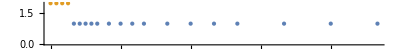

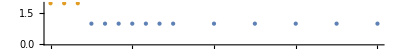

```mathematica
FloatsPlot[b_,p_,emin_,emax_,opts___]:=
NumberLinePlot[{
N[FloatsList[b,p,emin,emax]],
N[FloatsDenormList[b,p,emin]]}]

FloatsPlot[2,3,-1,2]
FloatsPlot[3,2,0,1]
```

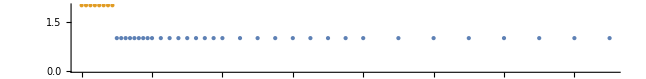

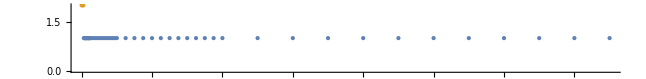

```mathematica
FloatsPlot[2,4,-1,2]
FloatsPlot[4,2,-1,2]
```